## 1. Инструменты имитационного моделирования

### 1.1. Данные

Импортируем пакеты. В них содержатся основные функции для работы

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["OptimizationPackage`"]
Needs["RequestFlowPackage`"]
Needs["SellerPackage`"]
```

Задаём контекст задачи: количество продуктов и рейсов, матрица принадлежности, цены, спрос (как список целых чисел или как набор распределений), вместимость самолётов и число экспериментов (для модели RLP)

```mathematica
context =<|
"numberOfProducts"->6,
"numberOfFlights"->2,
"membershipMatrix"->{{1,1,0,0,1,1},{0,0,1,1,1,1}}, 
"fares"->{40,24,70,42,100,60},
"demand"->(NormalDistribution[#,.2#]&/@{15,25,30,40,10,22}),
"capacity"->{50,70},
"numberOfExperiments"->1000
|>;
```

### 1.2. Расчёт оптимальных пределов бронирования

Сейчас в модели реализованы следующие подходы: DLP, PNLP, RLP, и они же с “умным” округлением. Если передать неправильный аргумент, будет выведено сообщение об ошибке.

```mathematica
SeedRandom[42];
FindBookingLimits[context]
FindBookingLimits[context,Model->"DLP"]
FindBookingLimits[context,Model->"PNLP"]
FindBookingLimits[context,Model->"RLP"]
FindBookingLimits[context,Model->"Round PNLP"]
bookingLimits=FindBookingLimits[context,Model->"Round RLP"]
FindBookingLimits[context,Model->"EMSR"]
FindBookingLimits[context,Model->"Unknown"]
```

{15,25,30,30,10,0}

{15,25,30,30,10,0}

{15.,19.1611,30.,24.1611,10.,5.83892}

{14.8212,22.0449,30.2933,26.5726,10.0299,3.10399}

{15,20,30,25,10,5}

{16,21,30,27,11,2}

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve::ifun will be suppressed during this calculation.

{50,35,70,46,0,0}

FindBookingLimits::option: Wrong model. Could be DLP, PNLP, Round PNLP, RLP or Round RLP. Got Unknown

FindBookingLimits[<|numberOfProducts→6,numberOfFlights→2,membershipMatrix→{{1,1,0,0,1,1},{0,0,1,1,1,1}},fares→{40,24,70,42,100,60},demand→{NormalDistribution[15,3.],NormalDistribution[25,5.],NormalDistribution[30,6.],NormalDistribution[40,8.],NormalDistribution[10,2.],NormalDistribution[22,4.4]},capacity→{50,70},numberOfExperiments→1000|>,Model→Unknown]

### 1.2. Генерация заявок

Возможны различные варианты: число заявок можно передать как список целых чисел или распределений. Если передать “плохое” распределение, будет выводиться сообщение об ошибке.

```mathematica
SeedRandom[42];
RequestFlow[6, 90,{2,3,4,1,7,5}, ConstantArray[UniformDistribution[{0,90}],6]]
requestFlow=RequestFlow[6, 90,{15,25,30,40,10,22}, ConstantArray[UniformDistribution[{0,90}],6]];
RequestFlow[6, 90,PoissonDistribution/@{2,3,4,1,7,5}, Table[TriangularDistribution[{0,90},c],{c,15,90,15}]]
RequestFlow[6, 90,NormalDistribution[#,.2#]&/@{2,3,4,1,7,5}, ConstantArray[UniformDistribution[{0,90}],6]](*Неправильный аргумент*)
```

{{3.45281,6},{18.5767,3},{23.2916,5},{26.0252,3},{26.6579,6},{26.7163,3},{29.2653,3},{31.2362,2},{33.8514,6},{35.1921,1},{38.3315,1},{40.8367,2},{47.5328,6},{49.5523,5},{50.0367,2},{54.6617,6},{64.5558,5},{66.5303,5},{67.8917,5},{77.4314,5},{87.5992,4},{89.7269,5}}

{{13.0832,1},{18.3215,3},{20.0985,4},{21.2888,3},{22.7962,3},{30.2832,2},{30.7137,4},{34.3984,5},{36.1489,3},{39.9087,2},{53.2853,5},{60.791,3},{61.6007,5},{64.7774,5},{65.2807,5},{69.0501,6},{71.0495,5},{71.767,5},{74.7322,1},{76.2637,5},{78.172,5},{83.836,6},{84.4263,5},{88.654,3}}

Private`readNumberOfRequests::argx: Wrong numberOfRequests argument. Could be list of integers or distributions, or multidimensial distribution. If distribution, each sample must be the list of nonnegative inetegers size 6

MapThread::mptd: Object Private`readNumberOfRequests[6,{1.63337,2.75731,2.44592,1.05153,6.25919,5.9273}] at position {2, 2} in MapThread[RandomVariate,{{UniformDistribution[{0,90}],UniformDistribution[{0,90}],UniformDistribution[{0,90}],UniformDistribution[{0,90}],UniformDistribution[{0,90}],UniformDistribution[{0,90}]},Private`readNumberOfRequests[6,{1.63337,2.75731,2.44592,1.05153,6.25919,5.9273}]}] has only 0 of required 1 dimensions.

Private`writeRequestFlow::argx: Wrong requestTimeDistributions. Each sample must be member of [0, 90] interval.

Private`writeRequestFlow[6,90,{{RandomVariate,1}[2,2],{RandomVariate,1}[{UniformDistribution[{0,90}],UniformDistribution[{0,90}],UniformDistribution[{0,90}],UniformDistribution[{0,90}],UniformDistribution[{0,90}],UniformDistribution[{0,90}]},Private`readNumberOfRequests[6,{1.63337,2.75731,2.44592,1.05153,6.25919,5.9273}]]}]

### 1.3. Продажа билетов

Реализована как невложенная

```mathematica
orders=requestFlow⟦All,2⟧;
sales=Seller[bookingLimits,orders]
```

{{16,21,30,27,11,2},{15,21,30,27,11,2},{15,21,29,27,11,2},{15,21,29,26,11,2},{15,21,28,26,11,2},{15,21,27,26,11,2},{15,21,27,26,10,2},{15,21,27,26,10,1},{15,21,27,26,10,0},{15,20,27,26,10,0},{15,20,27,25,10,0},{15,20,27,24,10,0},{15,20,27,23,10,0},{15,20,27,23,9,0},{15,20,27,23,9,0},{15,20,27,23,8,0},{15,20,27,23,8,0},{15,19,27,23,8,0},{15,19,26,23,8,0},{15,19,25,23,8,0},{15,19,25,23,8,0},{15,18,25,23,8,0},{15,18,25,23,8,0},{15,18,25,22,8,0},{15,18,25,21,8,0},{15,18,25,20,8,0},{15,18,25,20,8,0},{15,18,24,20,8,0},{15,18,24,20,8,0},{14,18,24,20,8,0},{14,18,24,19,8,0},{14,18,23,19,8,0},{14,17,23,19,8,0},{14,16,23,19,8,0},{13,16,23,19,8,0},{13,16,22,19,8,0},{13,15,22,19,8,0},{13,15,22,18,8,0},{13,14,22,18,8,0},{12,14,22,18,8,0},{12,14,21,18,8,0},{12,14,20,18,8,0},{12,14,20,17,8,0},{12,14,19,17,8,0},{12,14,19,17,8,0},{12,14,19,16,8,0},{12,14,19,16,8,0},{12,13,19,16,8,0},{12,13,19,16,8,0},{12,13,19,16,8,0},{12,13,19,15,8,0},{12,13,19,14,8,0},{12,13,19,13,8,0},{12,13,18,13,8,0},{12,13,18,13,8,0},{11,13,18,13,8,0},{11,13,18,13,8,0},{11,13,17,13,8,0},{11,12,17,13,8,0},{11,12,17,12,8,0},{11,12,17,11,8,0},{11,11,17,11,8,0},{10,11,17,11,8,0},{10,10,17,11,8,0},{10,10,17,11,8,0},{10,10,17,10,8,0},{9,10,17,10,8,0},{9,10,17,9,8,0},{9,10,16,9,8,0},{9,10,16,9,8,0},{9,10,16,8,8,0},{9,10,15,8,8,0},{9,10,15,7,8,0},{9,9,15,7,8,0},{9,9,15,7,7,0},{9,9,15,7,6,0},{9,9,15,7,5,0},{9,9,15,7,4,0},{9,9,15,6,4,0},{9,9,15,6,3,0},{9,9,14,6,3,0},{9,9,13,6,3,0},{9,9,13,6,3,0},{9,8,13,6,3,0},{9,8,13,5,3,0},{9,8,12,5,3,0},{9,8,11,5,3,0},{9,8,11,4,3,0},{9,8,11,3,3,0},{9,7,11,3,3,0},{9,7,11,2,3,0},{9,7,11,1,3,0},{9,6,11,1,3,0},{9,6,10,1,3,0},{9,6,10,0,3,0},{9,6,9,0,3,0},{9,5,9,0,3,0},{9,5,8,0,3,0},{9,4,8,0,3,0},{9,4,8,0,3,0},{9,3,8,0,3,0},{9,3,8,0,3,0},{9,2,8,0,3,0},{9,2,7,0,3,0},{9,2,7,0,3,0},{9,2,7,0,3,0},{9,2,7,0,3,0},{9,2,6,0,3,0},{9,1,6,0,3,0},{9,1,5,0,3,0},{9,1,5,0,3,0},{8,1,5,0,3,0},{8,1,5,0,3,0},{8,0,5,0,3,0},{7,0,5,0,3,0},{7,0,5,0,3,0},{7,0,5,0,3,0},{7,0,4,0,3,0},{7,0,4,0,3,0},{7,0,3,0,3,0},{6,0,3,0,3,0},{6,0,3,0,3,0},{6,0,2,0,3,0},{6,0,2,0,2,0},{5,0,2,0,2,0},{4,0,2,0,2,0},{4,0,2,0,2,0},{4,0,2,0,2,0},{3,0,2,0,2,0},{3,0,2,0,2,0},{3,0,2,0,2,0},{3,0,2,0,2,0},{2,0,2,0,2,0},{2,0,2,0,2,0},{1,0,2,0,2,0},{1,0,2,0,2,0},{1,0,2,0,2,0},{1,0,2,0,2,0},{1,0,1,0,2,0},{1,0,1,0,2,0},{1,0,1,0,1,0},{1,0,1,0,1,0},{1,0,0,0,1,0}}

Расчёт прибыли ↓

```mathematica
Boole[Equal@@@Partition[sales,2,1]].context["fares"]⟦orders⟧
```

1842

... так и вложенная система продаж. В случае последней необходимо задать иерархию классов. Частично аргументы проверяются на адекватность.

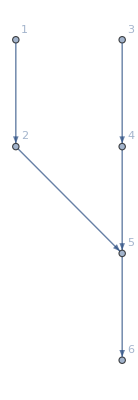

```mathematica
hierarchy={{1,2},{3,4},{5,6},{2,5},{4,5}};
Graph[hierarchy,DirectedEdges->True,VertexLabels->"Name"]
```

```mathematica
sales=Seller[context["membershipMatrix"],hierarchy,bookingLimits,orders,Nested->True];
DeleteCases[sales,{0..}]
```

{{16,21,30,27,11,2},{15,21,30,27,11,2},{15,21,29,27,11,2},{15,21,28,26,11,2},{15,21,27,26,11,2},{15,21,26,26,11,2},{14,20,25,25,10,2},{13,19,24,24,9,1},{12,18,23,23,8,0},{11,17,23,23,8,0},{11,17,22,22,8,0},{11,17,21,21,8,0},{11,17,20,20,8,0},{10,16,19,19,7,0},{9,15,18,18,6,0},{8,14,17,17,5,0},{7,13,16,16,4,0},{6,12,16,16,4,0},{6,12,15,15,4,0},{6,12,14,14,4,0},{5,11,13,13,3,0},{4,10,13,13,3,0},{3,9,12,12,2,0},{3,9,11,11,2,0},{3,9,10,10,2,0},{3,9,9,9,2,0},{2,8,8,8,1,0},{2,8,7,7,1,0},{1,7,6,6,0,0},{0,7,6,6,0,0},{0,7,5,5,0,0},{0,7,4,4,0,0},{0,6,4,4,0,0},{0,5,4,4,0,0},{0,5,4,4,0,0},{0,5,3,3,0,0},{0,4,3,3,0,0},{0,4,2,2,0,0},{0,3,2,2,0,0},{0,3,2,2,0,0},{0,3,1,1,0,0},{0,3,0,0,0,0},{0,3,0,0,0,0},{0,3,0,0,0,0},{0,2,0,0,0,0},{0,2,0,0,0,0},{0,1,0,0,0,0}}

Убедимся, что прибыль в разы выросла

```mathematica
Boole[Equal@@@Partition[sales,2,1]].context["fares"]⟦orders⟧
```

5050